```mathematica
(*Get pl-digits (for p=l the p-adic expansion) and the funny p power (just p^k for p=l)*)
pldigits[n_,p_,l_]:=If[n<l,{n},Append[IntegerDigits[(n-Mod[n,l])/l,p],IntegerDigits[n,l][[-1]]]];
frompldigits[n_,p_,l_]:=n[[-1]]+Sum[n[[-2-m]]*p^(m)*l,{m,0,Length[n]-2}];
(*Support etc., for pl-digits; this is [tilting:weyl] where n=highest weight*)
Support[n_,p_,l_]:=Module[
{res={{First[pldigits[n,p,l]]}},
lis=pldigits[n,p,l],
i,
le=Length[pldigits[n,p,l]],
copy1={},
copy2={}},
For[i=2,i≤le,i++,
copy1={};
copy2={};
Do[AppendTo[copy1,Append[el,lis[[i]]]],{el,res}];
If[lis[[i]]≠0,Do[AppendTo[copy2,Append[el,-lis[[i]]]],{el,res}]];
res=Join[copy1,copy2];
];
res
];
Delta[n_,p_,l_]:=Module[{nn={}},
nn=frompldigits[#,p,l]&/@Support[n+1,p,l];
Sort[nn-1]];
(*fusion rules using heighst weight notation, i.e. 3 means Delta(3) of highest weight 3; Tprod gives tiltings of the corresponding heighest weight, while DeltaProd is the classical rule and TProdDelta is assuming that T(m) and T(n) are a direct sum of Deltas (so generically)*)
DeltaProd[m_,n_]:=Table[i,{i,Abs[m-n],m+n,2}];
TProdDelta[m_,n_,p_,l_]:=Module[
{lm=Length[Delta[m,p,l]],
ln=Length[Delta[n,p,l]],
dm=Delta[m,p,l],
dn=Delta[n,p,l],
res={}},
For[i=1,i≤lm,i++,
For[j=1,j≤ln,j++,
res=Join[res,DeltaProd[dm[[i]],dn[[j]]]]
]];
Sort[res]
];
TProd[m_,n_,p_,l_]:=Module[
{li=TProdDelta[m,n,p,l],
hw=-1,
res={}},
While[Unequal[li ,{}],
hw=li[[-1]];
res=Join[res,{hw}];
For[ii=Length[Delta[hw,p,l]], ii≥1,ii--,
li=Drop[li,Position[li,Delta[hw,p,l][[ii]]][[1]]]
];
];
res=Sort[res];
res
];
(*Computes T(1)^(\otimes d) and dim space of invariants*)
ToneProd[d_,p_,l_]:=Module[
{out={0}},
For[jj=1,jj<d+1,jj++,
out=Flatten[TProd[1,#,p,l]&/@out]
];
out=Sort[out];
out
];
(*Set starting values for small p to have a faster calculation*)
smallvalues[p_]:=Switch[p,
2,{1,1,1},
3,{1,1,2,2,5},
5,{1,1,2,3,6,9,19,28,62},
7,{1,1,2,3,6,10,20,34,69,117,242,407,858},
11,{1,1,2,3,6,10,20,35,70,126,252,461,923,1703,3418,6330,12750,23630,47804,88502,179911}];
(*The bn function*)
bn[n_,p_]:=If[p>11,Length[ToneProd[n,p,p]],smallvalues[p][[n+1]]];
(*Polynomials for the recursion*)
P[x_,p_]:=2*ChebyshevT[p,x/2];
R[x_,i_,p_]:=If[i==0,1/2*(ChebyshevU[i,x/2]-ChebyshevU[i-2,x/2])*ChebyshevU[p-1,x/2],(ChebyshevU[i,x/2]-ChebyshevU[i-2,x/2])*ChebyshevU[p-1,x/2]];
Poly[x_,n_,i_,p_]:=R[x,i,p]*P[x,p]^(n)//Expand;
(*bn via recursion*)
bnrecursion[n_,p_]:=Module[{out={},runner=0,poly=1,k=0,list={}},
For[ij=0,ij<n+1,ij++,
If[ij<=2p-2,(runner=bn[ij,p];Goto[end])];
counter:=Mod[ij,p];
m:=(ij-counter)/p;
If[counter==p-1,poly=-(Poly[x,m,p-counter-1,p]-x^(ij)-x^(m)),poly=-(Poly[x,m-1,counter+1,p]-x^(ij)-x^(m-1))];
k=Exponent[poly,x];
list=CoefficientList[poly,x];
runner=Sum[list[[j+1]]*out[[j+1]],{j,0,k}];
Label[end];
out=Append[out,runner];
];
out
];
(*The growth rate*)
growth[n_,p_,a_]:=Table[If[i==0,1,a*i^(-1/2*Log[p,2*p^(2)/(p+1)])*2^(i)],{i,0,n}];
```

```mathematica
EmbedCode[CloudDeploy[Magnify[Manipulate[Show[ListLogPlot[{bnrecursion[n,p],growth[n,p,1]},PlotStyle->{Purple,Green},PlotLegends->Placed[{"bn","n^(α)2^n"},{0.85,0.25}],Joined->True],Graphics[Text["α="-1/2*Log[p,2*p^(2)/(p+1)]//N,{n/1.9,n/1.9}]]],{{n,10},0,100,Appearance->"Open"},{{p,3},{2,3,5,7,11}},LabelStyle->{15}]2],Permissions->"Public"]]
```

```mathematica
EmbedCode[CloudDeploy[Magnify[Manipulate[bnrecursion[n,p],{{n,10},0,100,Appearance->"Open"},{{p,3},{2,3,5,7,11}},LabelStyle->{15}]2],Permissions->"Public"]]
```

```mathematica
Manipulate[Show[ListLogPlot[{bnrecursion[n,p],growth[n,p,1]},PlotStyle->{Purple,Green},PlotLegends->Placed[{"bn","n^(α)2^n"},{0.85,0.25}],Joined->True],Graphics[Text["α="-1/2*Log[p,2*p^(2)/(p+1)]//N,{n/1.9,n/1.9}]]],{{n,10},0,100,Appearance->"Open"},{{p,3},{2,3,5,7,11}},LabelStyle->{15}]
```

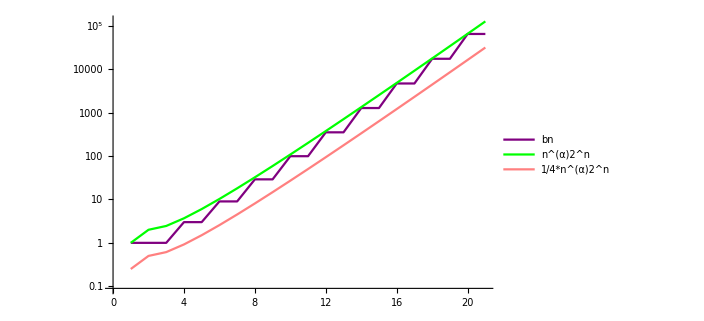

```mathematica
ListLogPlot[{bnrecursion[20,2],growth[20,2,1],1/4*growth[20,2,1]},PlotStyle->{Purple,Green,Pink},PlotLegends->Placed[{"bn","n^(α)2^n","1/4*n^(α)2^n"},{0.85,0.25}],Joined->True]
```

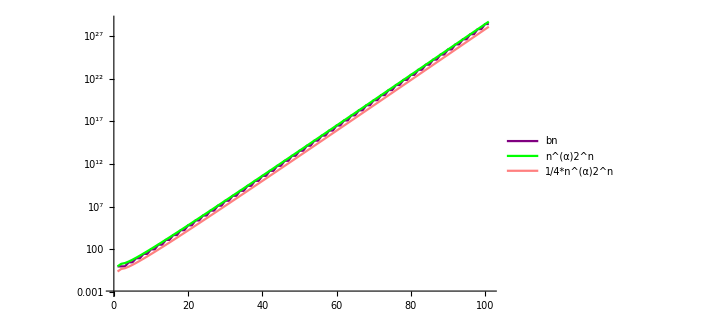

```mathematica
ListLogPlot[{bnrecursion[100,2],growth[100,2,1],1/4*growth[100,2,1]},PlotStyle->{Purple,Green,Pink},PlotLegends->Placed[{"bn","n^(α)2^n","1/4*n^(α)2^n"},{0.85,0.25}],Joined->True]
```

```mathematica
N[bnrecursion[100,2]*Table[2^(-n),{n,0,100}],10]
```

{1.,0.5,0.25,0.375,0.1875,0.28125,0.140625,0.2265625,0.11328125,0.193359375,0.0966796875,0.1713867188,0.08569335938,0.1553955078,0.07769775391,0.142791748,0.07139587402,0.1323013306,0.06615066528,0.1232852936,0.06164264679,0.1154036522,0.0577018261,0.1084553003,0.05422765017,0.102303952,0.05115197599,0.09684496373,0.04842248186,0.09199099429,0.04599549714,0.08766601281,0.04383300641,0.08380281262,0.04190140631,0.0803418796,0.0401709398,0.07723071389,0.03861535695,0.0744232618,0.0372116309,0.0718793515,0.03593967575,0.06956411719,0.0347820586,0.06744742537,0.03372371268,0.06550332131,0.03275166066,0.06370950993,0.03185475497,0.06204687963,0.03102343981,0.06049907315,0.03024953658,0.05905210587,0.02952605294,0.05769402962,0.02884701481,0.05641463907,0.02820731953,0.05520521673,0.02760260836,0.05405831267,0.02702915634,0.05296755497,0.02648377749,0.05192748708,0.02596374354,0.05093342873,0.02546671437,0.04998135728,0.02499067864,0.0490678066,0.0245339033,0.04818978121,0.0240948906,0.04734468334,0.02367234167,0.04653025121,0.0232651256,0.04574450677,0.02287225339,0.04498571158,0.02249285579,0.04425232958,0.02212616479,0.0435429957,0.02177149785,0.0428564895,0.02142824475,0.042191713,0.0210958565,0.04154767202,0.02077383601,0.04092346063,0.02046173032,0.04031824805,0.02015912402,0.03973126771,0.01986563386}